Section  II A : two well model, pg 2

```mathematica
(*hamiltonian with splitting a and interaction mu*)
Ham=
{{a+μ,-a/2,-a/2,0},{-a/2,a,0,-a/2},{-a/2,0,a,-a/2},{0,-a/2,-a/2,a+μ}};
N[Eigenvectors[Ham]/.{a->1,μ->4}]
N[Eigenvalues[Ham]/.{a->1,μ->4}]
```

{{0.,-1.,1.,0.},{-1.,0.,0.,1.},{1.,4.23607,4.23607,1.},{1.,-0.236068,-0.236068,1.}}

{1.,5.,0.763932,5.23607}

{(ⅇ^(-1/2 ⅈ t (2 (a+μ)+√(4 a^2+μ^2))) (2 a ⅇ^((ⅈ t μ)/2) (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (xy+yx)+2 ⅇ^(1/2 ⅈ t √(4 a^2+μ^2)) (x-y) √(4 a^2+μ^2)+ⅇ^(1/2 ⅈ t (μ+2 √(4 a^2+μ^2))) (x+y) (-μ+√(4 a^2+μ^2))+ⅇ^((ⅈ t μ)/2) (x+y) (μ+√(4 a^2+μ^2))))/(4 √(4 a^2+μ^2)),(ⅇ^(-1/2 ⅈ t (2 a+μ+√(4 a^2+μ^2))) (2 a (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (x+y)-xy μ-yx μ+xy √(4 a^2+μ^2)+2 ⅇ^(1/2 ⅈ t (μ+√(4 a^2+μ^2))) (xy-yx) √(4 a^2+μ^2)+yx √(4 a^2+μ^2)+ⅇ^(ⅈ t √(4 a^2+μ^2)) (xy+yx) (μ+√(4 a^2+μ^2))))/(4 √(4 a^2+μ^2)),(ⅇ^(-1/2 ⅈ t (2 a+μ+√(4 a^2+μ^2))) (2 a (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (x+y)-xy μ-yx μ+xy √(4 a^2+μ^2)-2 ⅇ^(1/2 ⅈ t (μ+√(4 a^2+μ^2))) (xy-yx) √(4 a^2+μ^2)+yx √(4 a^2+μ^2)+ⅇ^(ⅈ t √(4 a^2+μ^2)) (xy+yx) (μ+√(4 a^2+μ^2))))/(4 √(4 a^2+μ^2)),(ⅇ^(-1/2 ⅈ t (2 (a+μ)+√(4 a^2+μ^2))) (2 a ⅇ^((ⅈ t μ)/2) (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (xy+yx)-2 ⅇ^(1/2 ⅈ t √(4 a^2+μ^2)) (x-y) √(4 a^2+μ^2)+ⅇ^(1/2 ⅈ t (μ+2 √(4 a^2+μ^2))) (x+y) (-μ+√(4 a^2+μ^2))+ⅇ^((ⅈ t μ)/2) (x+y) (μ+√(4 a^2+μ^2))))/(4 √(4 a^2+μ^2))}

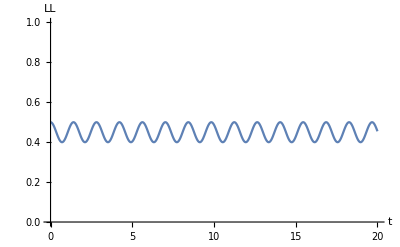

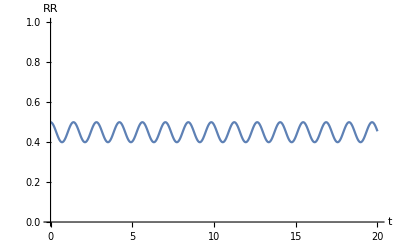

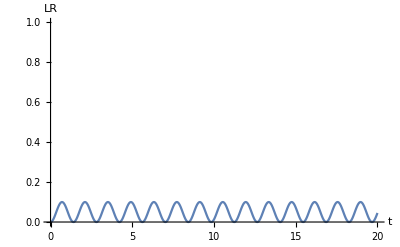

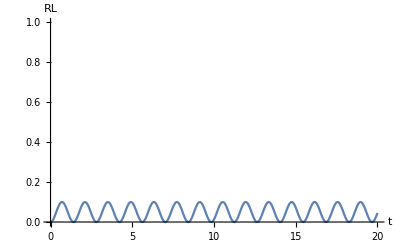

```mathematica
(*number counting operator, for number in the left well*)
NN={{2,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}};
(*state with both particles in left well*)
LL={1,0,0,0};
init = {x,xy,yx,y};
(*now evolve state*)
(*state=FullSimplify[  MatrixExp[-ⅉ Ham t].LL   ,Assumptions->t ∈ Reals]*)
state=FullSimplify[  MatrixExp[-ⅉ Ham t].init   ,Assumptions->t ∈ Reals]

(*decomposition of state occupation into LL RR LR and RL, see that when start in LL go between LL and RR superposition with only very small oscillating contribution from LR and RL. when start in RL do vice versa *)
Plot[Abs[state[[1]]]^2/.{a->1,μ->4,x->1/Sqrt[2],y->1/Sqrt[2],xy->0,yx->0},
{t,0,20},
AxesLabel->{"t","LL"},PlotRange->{0,1}]
Plot[Abs[state[[4]]]^2/.{a->1,μ->4,x->1/Sqrt[2],y->1/Sqrt[2],xy->0,yx->0},
{t,0,20},
AxesLabel->{"t","RR"},PlotRange->{0,1}]
Plot[Abs[state[[2]]]^2/.{a->1,μ->4,x->1/Sqrt[2],y->1/Sqrt[2],xy->0,yx->0},
{t,0,20},
AxesLabel->{"t","LR"},PlotRange->{0,1}]
Plot[Abs[state[[3]]]^2/.{a->1,μ->4,x->1/Sqrt[2],y->1/Sqrt[2],xy->0,yx->0},
{t,0,20},
AxesLabel->{"t","RL"},PlotRange->{0,1}]
```

this is the same as the paper just written differently idk:

```mathematica
expectN = FullSimplify[ConjugateTranspose[state].NN .state ,Assumptions->{a∈ Reals,μ∈ Reals,t∈ Reals}]
(*Replace[expectN,√(4 a^2+μ^2)->b]*) ; 


(*paper = FullSimplify[1+(√(4 a^2+m^2)-m)/(2 √(4 a^2+m^2))Cos[(√(4 a^2+m^2)+m)/2 t]+(√(4 a^2+m^2)+m)/(2 √(4 a^2+m^2))Cos[(√(4 a^2+m^2)-m)/2 t]/.√(4 a^2+m^2)->b];
paper=Replace[paper, Sqrt[4 a^2+m^2]->b]//FullSimplify *)
```

1/(16 (4 a^2+μ^2))(2 (2 a ⅇ^((ⅈ t μ)/2) (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (xy+yx)+2 ⅇ^(1/2 ⅈ t √(4 a^2+μ^2)) (x-y) √(4 a^2+μ^2)+ⅇ^(1/2 ⅈ t (μ+2 √(4 a^2+μ^2))) (x+y) (-μ+√(4 a^2+μ^2))+ⅇ^((ⅈ t μ)/2) (x+y) (μ+√(4 a^2+μ^2))) Conjugate[2 a ⅇ^((ⅈ t μ)/2) (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (xy+yx)+2 ⅇ^(1/2 ⅈ t √(4 a^2+μ^2)) (x-y) √(4 a^2+μ^2)+ⅇ^(1/2 ⅈ t (μ+2 √(4 a^2+μ^2))) (x+y) (-μ+√(4 a^2+μ^2))+ⅇ^((ⅈ t μ)/2) (x+y) (μ+√(4 a^2+μ^2))]+(2 a (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (x+y)-xy μ-yx μ+xy √(4 a^2+μ^2)-2 ⅇ^(1/2 ⅈ t (μ+√(4 a^2+μ^2))) (xy-yx) √(4 a^2+μ^2)+yx √(4 a^2+μ^2)+ⅇ^(ⅈ t √(4 a^2+μ^2)) (xy+yx) (μ+√(4 a^2+μ^2))) Conjugate[2 a (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (x+y)-xy μ-yx μ+xy √(4 a^2+μ^2)-2 ⅇ^(1/2 ⅈ t (μ+√(4 a^2+μ^2))) (xy-yx) √(4 a^2+μ^2)+yx √(4 a^2+μ^2)+ⅇ^(ⅈ t √(4 a^2+μ^2)) (xy+yx) (μ+√(4 a^2+μ^2))]+(2 a (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (x+y)-xy μ-yx μ+xy √(4 a^2+μ^2)+2 ⅇ^(1/2 ⅈ t (μ+√(4 a^2+μ^2))) (xy-yx) √(4 a^2+μ^2)+yx √(4 a^2+μ^2)+ⅇ^(ⅈ t √(4 a^2+μ^2)) (xy+yx) (μ+√(4 a^2+μ^2))) Conjugate[2 a (-1+ⅇ^(ⅈ t √(4 a^2+μ^2))) (x+y)-xy μ-yx μ+xy √(4 a^2+μ^2)+2 ⅇ^(1/2 ⅈ t (μ+√(4 a^2+μ^2))) (xy-yx) √(4 a^2+μ^2)+yx √(4 a^2+μ^2)+ⅇ^(ⅈ t √(4 a^2+μ^2)) (xy+yx) (μ+√(4 a^2+μ^2))])

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
ComplexExpand[expectN]
```

xy^2/8+(xy yx)/4+yx^2/8+(a^2 x^2)/(2 (4 a^2+μ^2))+(a^2 x y)/(4 a^2+μ^2)+(a^2 y^2)/(2 (4 a^2+μ^2))+(a x xy μ)/(2 (4 a^2+μ^2))+(a xy y μ)/(2 (4 a^2+μ^2))+(a x yx μ)/(2 (4 a^2+μ^2))+(a y yx μ)/(2 (4 a^2+μ^2))+(xy^2 μ^2)/(8 (4 a^2+μ^2))+(xy yx μ^2)/(4 (4 a^2+μ^2))+(yx^2 μ^2)/(8 (4 a^2+μ^2))-(a x xy)/(2 √(4 a^2+μ^2))-(a xy y)/(2 √(4 a^2+μ^2))-(a x yx)/(2 √(4 a^2+μ^2))-(a y yx)/(2 √(4 a^2+μ^2))-(xy^2 μ)/(4 √(4 a^2+μ^2))-(xy yx μ)/(2 √(4 a^2+μ^2))-(yx^2 μ)/(4 √(4 a^2+μ^2))+1/8 x^2 Cos[(t μ)/2]^2+1/4 x y Cos[(t μ)/2]^2+1/8 y^2 Cos[(t μ)/2]^2+(a^2 xy^2 Cos[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(a^2 xy yx Cos[(t μ)/2]^2)/(4 a^2+μ^2)+(a^2 yx^2 Cos[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a x xy μ Cos[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a xy y μ Cos[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a x yx μ Cos[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a y yx μ Cos[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(x^2 μ^2 Cos[(t μ)/2]^2)/(8 (4 a^2+μ^2))+(x y μ^2 Cos[(t μ)/2]^2)/(4 (4 a^2+μ^2))+(y^2 μ^2 Cos[(t μ)/2]^2)/(8 (4 a^2+μ^2))-(a x xy Cos[(t μ)/2]^2)/(2 √(4 a^2+μ^2))-(a xy y Cos[(t μ)/2]^2)/(2 √(4 a^2+μ^2))-(a x yx Cos[(t μ)/2]^2)/(2 √(4 a^2+μ^2))-(a y yx Cos[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(x^2 μ Cos[(t μ)/2]^2)/(4 √(4 a^2+μ^2))+(x y μ Cos[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(y^2 μ Cos[(t μ)/2]^2)/(4 √(4 a^2+μ^2))+1/2 x^2 Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)]-1/2 y^2 Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)]-(a x xy Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a xy y Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a x yx Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a y yx Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(x^2 μ Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))-(y^2 μ Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))+1/2 x^2 Cos[1/2 t √(4 a^2+μ^2)]^2-x y Cos[1/2 t √(4 a^2+μ^2)]^2+1/2 y^2 Cos[1/2 t √(4 a^2+μ^2)]^2+1/4 xy^2 Cos[t √(4 a^2+μ^2)]+1/2 xy yx Cos[t √(4 a^2+μ^2)]+1/4 yx^2 Cos[t √(4 a^2+μ^2)]-(a^2 x^2 Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(2 a^2 x y Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(a^2 y^2 Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(a x xy μ Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(a xy y μ Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(a x yx μ Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(a y yx μ Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(xy^2 μ^2 Cos[t √(4 a^2+μ^2)])/(4 (4 a^2+μ^2))-(xy yx μ^2 Cos[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))-(yx^2 μ^2 Cos[t √(4 a^2+μ^2)])/(4 (4 a^2+μ^2))-(a^2 xy^2 Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(2 a^2 xy yx Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)-(a^2 yx^2 Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(4 a^2+μ^2)+(a x xy μ Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))+(a xy y μ Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))+(a x yx μ Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))+(a y yx μ Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))+(a x xy Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))+(a xy y Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))+(a x yx Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))+(a y yx Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))+(a x xy Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)] Cos[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a xy y Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)] Cos[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a x yx Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)] Cos[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a y yx Cos[(t μ)/2] Cos[1/2 t √(4 a^2+μ^2)] Cos[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+1/8 xy^2 Cos[t √(4 a^2+μ^2)]^2+1/4 xy yx Cos[t √(4 a^2+μ^2)]^2+1/8 yx^2 Cos[t √(4 a^2+μ^2)]^2+(a^2 x^2 Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a^2 x y Cos[t √(4 a^2+μ^2)]^2)/(4 a^2+μ^2)+(a^2 y^2 Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a x xy μ Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a xy y μ Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a x yx μ Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a y yx μ Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(xy^2 μ^2 Cos[t √(4 a^2+μ^2)]^2)/(8 (4 a^2+μ^2))+(xy yx μ^2 Cos[t √(4 a^2+μ^2)]^2)/(4 (4 a^2+μ^2))+(yx^2 μ^2 Cos[t √(4 a^2+μ^2)]^2)/(8 (4 a^2+μ^2))+(a x xy Cos[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(a xy y Cos[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(a x yx Cos[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(a y yx Cos[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(xy^2 μ Cos[t √(4 a^2+μ^2)]^2)/(4 √(4 a^2+μ^2))+(xy yx μ Cos[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(yx^2 μ Cos[t √(4 a^2+μ^2)]^2)/(4 √(4 a^2+μ^2))+(a^2 xy^2 Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a^2 xy yx Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)]^2)/(4 a^2+μ^2)+(a^2 yx^2 Cos[(t μ)/2]^2 Cos[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+1/2 xy^2 Cos[1/2 t (μ+√(4 a^2+μ^2))]^2-xy yx Cos[1/2 t (μ+√(4 a^2+μ^2))]^2+1/2 yx^2 Cos[1/2 t (μ+√(4 a^2+μ^2))]^2+1/4 x^2 Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))]+1/2 x y Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))]+1/4 y^2 Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))]+(a x xy μ Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a xy y μ Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a x yx μ Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a y yx μ Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(x^2 μ^2 Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(4 (4 a^2+μ^2))-(x y μ^2 Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(y^2 μ^2 Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(4 (4 a^2+μ^2))-(a x xy Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a xy y Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a x yx Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a y yx Cos[(t μ)/2] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+1/2 x^2 Cos[1/2 t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))]-1/2 y^2 Cos[1/2 t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))]-(x^2 μ Cos[1/2 t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(y^2 μ Cos[1/2 t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a x xy μ Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a xy y μ Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a x yx μ Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a y yx μ Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a x xy Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a xy y Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a x yx Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a y yx Cos[(t μ)/2] Cos[t √(4 a^2+μ^2)] Cos[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+1/8 x^2 Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2+1/4 x y Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2+1/8 y^2 Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2+(x^2 μ^2 Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(8 (4 a^2+μ^2))+(x y μ^2 Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(4 (4 a^2+μ^2))+(y^2 μ^2 Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(8 (4 a^2+μ^2))-(x^2 μ Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(4 √(4 a^2+μ^2))-(x y μ Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(2 √(4 a^2+μ^2))-(y^2 μ Cos[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(4 √(4 a^2+μ^2))+1/8 x^2 Sin[(t μ)/2]^2+1/4 x y Sin[(t μ)/2]^2+1/8 y^2 Sin[(t μ)/2]^2+(a^2 xy^2 Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(a^2 xy yx Sin[(t μ)/2]^2)/(4 a^2+μ^2)+(a^2 yx^2 Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a x xy μ Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a xy y μ Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a x yx μ Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))-(a y yx μ Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(x^2 μ^2 Sin[(t μ)/2]^2)/(8 (4 a^2+μ^2))+(x y μ^2 Sin[(t μ)/2]^2)/(4 (4 a^2+μ^2))+(y^2 μ^2 Sin[(t μ)/2]^2)/(8 (4 a^2+μ^2))-(a x xy Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))-(a xy y Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))-(a x yx Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))-(a y yx Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(x^2 μ Sin[(t μ)/2]^2)/(4 √(4 a^2+μ^2))+(x y μ Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(y^2 μ Sin[(t μ)/2]^2)/(4 √(4 a^2+μ^2))-(a^2 xy^2 Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(4 a^2+μ^2)-(2 a^2 xy yx Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(4 a^2+μ^2)-(a^2 yx^2 Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(4 a^2+μ^2)+(a x xy μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(a xy y μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(a x yx μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(a y yx μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(a x xy Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(a xy y Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(a x yx Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(a y yx Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2]^2)/(2 √(4 a^2+μ^2))+(a^2 xy^2 Cos[t √(4 a^2+μ^2)]^2 Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+(a^2 xy yx Cos[t √(4 a^2+μ^2)]^2 Sin[(t μ)/2]^2)/(4 a^2+μ^2)+(a^2 yx^2 Cos[t √(4 a^2+μ^2)]^2 Sin[(t μ)/2]^2)/(2 (4 a^2+μ^2))+1/2 x^2 Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)]-1/2 y^2 Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)]-(a x xy Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a xy y Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a x yx Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a y yx Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(x^2 μ Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))-(y^2 μ Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))+(a x xy Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a xy y Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a x yx Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a y yx Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+1/2 x^2 Sin[1/2 t √(4 a^2+μ^2)]^2-x y Sin[1/2 t √(4 a^2+μ^2)]^2+1/2 y^2 Sin[1/2 t √(4 a^2+μ^2)]^2-(a x xy Cos[1/2 t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a xy y Cos[1/2 t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a x yx Cos[1/2 t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a y yx Cos[1/2 t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a x xy μ Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))+(a xy y μ Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))+(a x yx μ Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))+(a y yx μ Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 (4 a^2+μ^2))-(a x xy Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))-(a xy y Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))-(a x yx Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))-(a y yx Cos[1/2 t (μ+2 √(4 a^2+μ^2))] Sin[(t μ)/2] Sin[t √(4 a^2+μ^2)])/(2 √(4 a^2+μ^2))+(a x xy Cos[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a xy y Cos[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+(a x yx Cos[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))-(a y yx Cos[(t μ)/2] Sin[1/2 t √(4 a^2+μ^2)] Sin[t √(4 a^2+μ^2)])/(√(4 a^2+μ^2))+1/8 xy^2 Sin[t √(4 a^2+μ^2)]^2+1/4 xy yx Sin[t √(4 a^2+μ^2)]^2+1/8 yx^2 Sin[t √(4 a^2+μ^2)]^2+(a^2 x^2 Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a^2 x y Sin[t √(4 a^2+μ^2)]^2)/(4 a^2+μ^2)+(a^2 y^2 Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a x xy μ Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a xy y μ Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a x yx μ Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a y yx μ Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(xy^2 μ^2 Sin[t √(4 a^2+μ^2)]^2)/(8 (4 a^2+μ^2))+(xy yx μ^2 Sin[t √(4 a^2+μ^2)]^2)/(4 (4 a^2+μ^2))+(yx^2 μ^2 Sin[t √(4 a^2+μ^2)]^2)/(8 (4 a^2+μ^2))+(a x xy Sin[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(a xy y Sin[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(a x yx Sin[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(a y yx Sin[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(xy^2 μ Sin[t √(4 a^2+μ^2)]^2)/(4 √(4 a^2+μ^2))+(xy yx μ Sin[t √(4 a^2+μ^2)]^2)/(2 √(4 a^2+μ^2))+(yx^2 μ Sin[t √(4 a^2+μ^2)]^2)/(4 √(4 a^2+μ^2))+(a^2 xy^2 Cos[(t μ)/2]^2 Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a^2 xy yx Cos[(t μ)/2]^2 Sin[t √(4 a^2+μ^2)]^2)/(4 a^2+μ^2)+(a^2 yx^2 Cos[(t μ)/2]^2 Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a^2 xy^2 Sin[(t μ)/2]^2 Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+(a^2 xy yx Sin[(t μ)/2]^2 Sin[t √(4 a^2+μ^2)]^2)/(4 a^2+μ^2)+(a^2 yx^2 Sin[(t μ)/2]^2 Sin[t √(4 a^2+μ^2)]^2)/(2 (4 a^2+μ^2))+1/2 xy^2 Sin[1/2 t (μ+√(4 a^2+μ^2))]^2-xy yx Sin[1/2 t (μ+√(4 a^2+μ^2))]^2+1/2 yx^2 Sin[1/2 t (μ+√(4 a^2+μ^2))]^2+1/4 x^2 Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))]+1/2 x y Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))]+1/4 y^2 Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))]+(a x xy μ Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a xy y μ Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a x yx μ Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a y yx μ Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(x^2 μ^2 Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(4 (4 a^2+μ^2))-(x y μ^2 Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(y^2 μ^2 Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(4 (4 a^2+μ^2))-(a x xy Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a xy y Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a x yx Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a y yx Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a x xy μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a xy y μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a x yx μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a y yx μ Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a x xy Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a xy y Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a x yx Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a y yx Cos[t √(4 a^2+μ^2)] Sin[(t μ)/2] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+1/2 x^2 Sin[1/2 t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))]-1/2 y^2 Sin[1/2 t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))]-(x^2 μ Sin[1/2 t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(y^2 μ Sin[1/2 t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))-(a x xy μ Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a xy y μ Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a x yx μ Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))-(a y yx μ Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 (4 a^2+μ^2))+(a x xy Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a xy y Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a x yx Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+(a y yx Cos[(t μ)/2] Sin[t √(4 a^2+μ^2)] Sin[1/2 t (μ+2 √(4 a^2+μ^2))])/(2 √(4 a^2+μ^2))+1/8 x^2 Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2+1/4 x y Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2+1/8 y^2 Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2+(x^2 μ^2 Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(8 (4 a^2+μ^2))+(x y μ^2 Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(4 (4 a^2+μ^2))+(y^2 μ^2 Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(8 (4 a^2+μ^2))-(x^2 μ Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(4 √(4 a^2+μ^2))-(x y μ Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(2 √(4 a^2+μ^2))-(y^2 μ Sin[1/2 t (μ+2 √(4 a^2+μ^2))]^2)/(4 √(4 a^2+μ^2))

```mathematica
Manipulate[Plot[expectN /.{a->1,x->0,y->0,xy->1/Sqrt[2],yx->1/Sqrt[2]},
{t,0,20},
AxesLabel->{"t","expected N_L(t) /2"},PlotRange->All],{μ,1,4}] (*,{x,0,1},{y,0,1},{xy,0,1},{yx,0,1}*)
```

```mathematica
(*this is the result of N_L from initial LL state*)
Manipulate[Plot[(1+Cos[(μ t)/2] Cos[1/2 √(4 a^2+μ^2) t]+(μ Sin[(μ t)/2] Sin[1/2 √(4 a^2+μ^2) t])/(√(4 a^2+μ^2)))/2
/.{a->1},
{t,0,20},
AxesLabel->{"t","expected N_L(t) /2"},PlotRange->All],
{μ,1,4}]
```